ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics3D-

-Graphics-

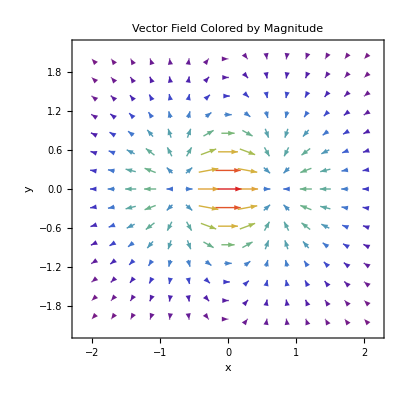

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A[x_,y_]=D[f[x,y],x]
B[x_,y_]=D[f[x,y],y]
Plot3D[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,PlotLegends->Automatic,ColorFunction->"Rainbow",AxesLabel->{"x","y"}]
ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"Rainbow"]
VectorPlot[{A[x,y],B[x,y]},{x,-2,2},{y,-2,2},VectorColorFunction->Function[{x,y,u,v,norm},ColorData["Rainbow"][norm]],VectorColorFunctionScaling->True,FrameLabel->{"x","y"},PlotLabel->"Vector Field Colored by Magnitude"]
```

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
grad=Grad[f[x,y],{x,y}]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic];
plot2=VectorPlot[grad,{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

{ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2,-2 ⅇ^(-x^2-y^2) x y}

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[{"TemperatureMap",{-5,5}}],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[{"TemperatureMap",{0,1}}],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,ContourLabels->True,PlotLegends->BarLegend[{"TemperatureMap",{0,1}}],(*Setting range in legend may show wrong data from the plot*)ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
A=D[f[x,y],x]
B=D[f[x,y],y]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->BarLegend[Automatic,None],ColorFunction->"TemperatureMap"];
plot2=VectorPlot[{A,B},{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2

-2 ⅇ^(-x^2-y^2) x y

-Graphics-

```mathematica
f[x_,y_]:=x Exp[-(x^2+y^2)];
grad=Grad[f[x,y],{x,y}]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"TemperatureMap"];
plot2=VectorPlot[grad,{x,-2,2},{y,-2,2},VectorStyle->Black];
Show[plot1,plot2]
```

{ⅇ^(-x^2-y^2)-2 ⅇ^(-x^2-y^2) x^2,-2 ⅇ^(-x^2-y^2) x y}

-Graphics-

```mathematica
G2[x_,y_,σ_]:=(1/((σ^2)*2Pi))Exp[-(((x-a)^2)+((y-b)^2))/(2σ^2)];
a=2;b=2;
grad=Grad[G2[x,y,σ],{x,y}]
Plot3D[G2[x,y,σ=0.5], {x, 0,4},{y,0,4},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"},ColorFunction->"Rainbow"]
plot1=ContourPlot[G2[x,y,σ=0.5], {x, 0,4},{y,0,4},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"Rainbow"];
plot2=VectorPlot[grad,{x,0,4},{y,0,4},VectorStyle->Black];
Show[plot1,plot2]
```

{-(ⅇ^((-(-2+x)^2-(-2+y)^2)/(2 σ^2)) (-2+x))/(2 π σ^4),-(ⅇ^((-(-2+x)^2-(-2+y)^2)/(2 σ^2)) (-2+y))/(2 π σ^4)}

-Graphics3D-

-Graphics-

```mathematica
g2[x_,y_]:=Exp[-x^2]+Exp[-y^2];
grad=Grad[g2[x,y],{x,y}]
Plot3D[g2[x,y], {x, -5,5},{y,-5,5},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"},ColorFunction->"Rainbow"]
plot1=ContourPlot[g2[x,y], {x, -5,5},{y,-5,5},PlotPoints->100,Contours->30,ContourStyle->Gray,PlotLegends->Automatic,ColorFunction->"Rainbow"];
plot2=VectorPlot[grad,{x,-5,5},{y,-5,5},VectorStyle->Black];
Show[plot1,plot2]
```

{-2 ⅇ^(-x^2) x,-2 ⅇ^(-y^2) y}

-Graphics3D-

-Graphics-

```mathematica
f[x_,y_]:=-((Cos[x])^2+(Cos[y])^2)^2;
grad=Grad[f[x,y],{x,y}]
Plot3D[f[x,y],{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2},Mesh->None,AxesLabel->{"x","y"}]
plot1=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100,Contours->30,ContourStyle->None,PlotLegends->Automatic,ColorFunction->"Rainbow",AxesLabel->{"x","y"}];
plot2=VectorPlot[grad,{x,-2,2},{y,-2,2},VectorStyle->Black,FrameLabel->{"x","y"}];
Show[plot1,plot2]
```

{4 Cos[x] (Cos[x]^2+Cos[y]^2) Sin[x],4 Cos[y] (Cos[x]^2+Cos[y]^2) Sin[y]}

-Graphics3D-

-Graphics-

```mathematica
f[x_,y_]:=-((Cos[x])^2+(Cos[y])^2)^2;
grad=Grad[f[x,y],{x,y}]
surface=Plot3D[f[x,y],{x, -Pi/2, Pi/2},{y,- Pi/2, Pi/2},PlotStyle->Opacity[0.7],Mesh->None];
vectorField=Graphics3D[Table[Arrow[{{x,y,0},{x+Cos[y],y+Sin[x],0}}],{x,-2 Pi,2 Pi,Pi/4},{y,-2 Pi,2 Pi,Pi/4}]];
Show[surface,vectorField,Boxed->True]
```

{4 Cos[x] (Cos[x]^2+Cos[y]^2) Sin[x],4 Cos[y] (Cos[x]^2+Cos[y]^2) Sin[y]}

-Graphics3D-

```mathematica
f[x_,y_]:=-((Cos[x])^2+(Cos[y])^2)^2;
grad=Grad[f[x,y],{x,y}]
surface=Plot3D[f[x,y],{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2},PlotStyle->Opacity[0.7],MeshFunctions->{#3&},MeshStyle->{{Thick,Gray}},AxesLabel->{"x","y","f(x, y)"}];

(*Create the 2D vector field*)
vectorField=VectorPlot[grad,{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2},Axes->False,Frame->False];

(*Combine the plots*)
Show[surface,Graphics3D[{Inset[vectorField,{0,0,0},{Center,Center},{6,6}]}],Boxed->True]
```

{4 Cos[x] (Cos[x]^2+Cos[y]^2) Sin[x],4 Cos[y] (Cos[x]^2+Cos[y]^2) Sin[y]}

-Graphics3D-